# Read Latency Comparison

## 2016-04-07 hengxin0912@gmail.com File: “~/mma-projects/RWN-latency/rwn-2am-read-latency.nb Online: https://github.com/hengxin/mma-projects/tree/master/2am/RWN-latency

```mathematica
ClearAll[latencyDir,rawLatencyDataRelativeDir,rawLatencyDataFullDir];
```

## Chapter 1: Procedures for Data Pre-processing

## Data Import:

```mathematica
dataImport[file_String]:=
Module[{data},
data=Select[Import[file,"Table"], First[#]==1&][[All,2]]
];
```

## Quantiles:

```mathematica
quantiles[data_List,quantile_List]:=
Module[{},
Quantile[data,quantile,{{1/2,0},{0,1}}]
];
```

## QuantilesAndMean:

```mathematica
quantilesAndMean[data_List,quantile_List]:=
Module[{},
Append[Quantile[data,quantile,{{1/2,0},{0,1}}],Round[Mean[data]]]
];
```

## Chapter 2: RWN vs. 2AM (and ABD)

## Directory:

```mathematica
rwnLatencyDir="~/mma-projects/2am/RWN-latency/";
rwnLatencyRawDataRelativeDir="rwn-latency-raw-data/";
rwnLatencyRawDataFullDir=rwnLatencyDir<>rwnLatencyRawDataRelativeDir;
SetDirectory[rwnLatencyRawDataFullDir];
```

## Quantiles for all RWN Executions:

```mathematica
quantilesAll=quantilesAndMean[dataImport[rwnLatencyRawDataFullDir<>#],{0,0.01,0.25,0.5,0.75,0.95,0.99,1.0}]&/@FileNames[];
```

## Export Data:

```mathematica
Export[rwnLatencyDir<>"rwn-2am-read-latency-quantiles.txt",quantilesAll, "Table"]
```

~/mma-projects/2am/RWN-latency/rwn-2am-read-latency-quantiles.txt

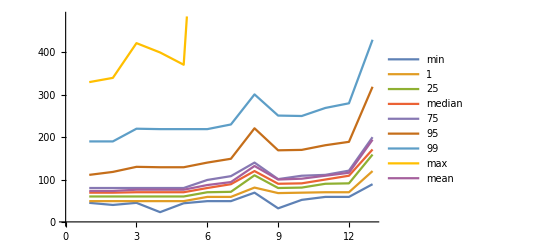

```mathematica
ListLinePlot[Transpose[quantilesAll],PlotLegends->{"min","1","25","median", "75","95","99", "max","mean"}]
```

## The remaining work is done with PGFPlots.

### See “https://bitbucket.org/hengxin/paper-tc-2am/src/87e53858b8635a6349cd627ba04f28155545bcbf/fig/rwn-2am-read-latency-quantiles.tex?at=tc-major-revision&fileviewer=file-view-default”

## Chapter 3: ABD vs. 2AM

```mathematica
ClearAll[abd2amLatencyDir,abd2amLatencyRawDataRelativeDir,abd2amLatencyRawDataFullDir]
```

## Directory:

```mathematica
abd2amLatencyDir="~/mma-projects/2am/ABD-2AM-latency/";
abd2amLatencyRawDataRelativeDir="abd-2am-latency-raw-data/";
abd2amLatencyRawDataFullDir=abd2amLatencyDir<>abd2amLatencyRawDataRelativeDir;
abd2amLatencyBoxplotStatRelativeDir="abd-2am-latency-boxplot-stat/";
abd2amLatencyBoxplotStatFullDir=abd2amLatencyDir<>abd2amLatencyBoxplotStatRelativeDir;
SetDirectory[abd2amLatencyRawDataFullDir];
FileNames[]
```

{rate50-replica2-2am.txt,rate50-replica2-abd.txt,rate50-replica3-2am.txt,rate50-replica3-abd.txt,rate50-replica4-2am.txt,rate50-replica4-abd.txt,rate50-replica5-2am.txt,rate50-replica5-abd.txt,rate5-replica2-2am.txt,rate5-replica2-abd.txt,rate5-replica3-2am.txt,rate5-replica3-abd.txt,rate5-replica4-2am.txt,rate5-replica4-abd.txt,rate5-replica5-2am.txt,rate5-replica5-abd.txt}

## Statistics for boxplot:

```mathematica
boxplotStat[data_List,quantile_List]:=
Module[{q,qMean},
q=Quantile[data,quantile,{{1/2,0},{0,1}}];
qMean=Append[q,Round[Mean[data]]];
qMean~Join~Select[data,#<First[q]||#>Last[q]&]
];
```

## AllInOne: Import, compute boxplot statistics, and export:

```mathematica
(*min,25th,median,75th,99th + mean*)
```

```mathematica
importComputAndExport[fromFile_String,toFile_String]:=
Module[{},
Export[
toFile,
boxplotStat[dataImport[fromFile],{0,0.25,0.5,0.75,0.99}],
"Table"
]
];
```

```mathematica
SetDirectory[abd2amLatencyRawDataFullDir];
```

```mathematica
importComputAndExport[abd2amLatencyRawDataFullDir<>#,abd2amLatencyBoxplotStatFullDir<>"boxplot-"<>#]&/@FileNames[]
```

Quantile::empt: Argument {} should be a non-empty list.

Quantile::argb: Quantile[{},{0,0.25,0.5,0.75,0.99},{{1/2,0},{0,1}},Round[Mean[{}]]] called with 4 arguments; between 2 and 3 arguments are expected.

Join::heads: Heads Quantile and List at positions 1 and 2 are expected to be the same.

Quantile::empt: Argument {} should be a non-empty list.

Quantile::argb: Quantile[{},{0,0.25,0.5,0.75,0.99},{{1/2,0},{0,1}},Round[Mean[{}]]] called with 4 arguments; between 2 and 3 arguments are expected.

Join::heads: Heads Quantile and List at positions 1 and 2 are expected to be the same.

Quantile::empt: Argument {} should be a non-empty list.

General::stop: Further output of Quantile::empt will be suppressed during this calculation.

Quantile::argb: Quantile[{},{0,0.25,0.5,0.75,0.99},{{1/2,0},{0,1}},Round[Mean[{}]]] called with 4 arguments; between 2 and 3 arguments are expected.

General::stop: Further output of Quantile::argb will be suppressed during this calculation.

Join::heads: Heads Quantile and List at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

{~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate50-replica2-2am-5000.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate50-replica2-2am-old.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate50-replica2-2am.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate50-replica2-abd-5000.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate50-replica2-abd-old.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate50-replica2-abd.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate50-replica3-2am.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate50-replica3-abd.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate50-replica4-2am.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate50-replica4-abd.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate50-replica5-2am.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate50-replica5-abd.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate5-replica2-2am-5000.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate5-replica2-2am-old.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate5-replica2-2am.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate5-replica2-abd-5000.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate5-replica2-abd-old.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate5-replica2-abd.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate5-replica3-2am.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate5-replica3-abd.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate5-replica4-2am.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate5-replica4-abd.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate5-replica5-2am.txt,~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-boxplot-stat/boxplot-rate5-replica5-abd.txt}

```mathematica
(* 
rename[dir_String]:=
Module[{},
SetDirectory[dir];
RenameDirectory[#,StringRiffle[(StringSplit[#,";"][[{5,7,2}]]),"-"]]&/@FileNames[];
];
*)
```

```mathematica
(* Copy data; overwritten if necessary *)
copyData[srcDir_String,toDir_String]:=
Module[{},
SetDirectory[srcDir];
CopyFile[FileNameJoin[{srcDir,#,"allinone","allinone_delay.txt"}],FileNameJoin[{toDir,#<>".txt"}], OverwriteTarget->True]&/@FileNames[]
];
```

```mathematica
copyData["/home/hengxin/android-studio-projects/distributed-mobile-memo/app/src/experimental-data/Raw data/ContactingAllForLatency","/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data"]
```

{/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate50-replica2-2am.txt,/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate50-replica2-2am-old.txt,/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate50-replica2-abd.txt,/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate50-replica2-abd-old.txt,/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate50-replica3-2am.txt,/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate50-replica3-abd.txt,/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate50-replica4-2am.txt,/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate50-replica4-abd.txt,/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate50-replica5-2am.txt,/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate50-replica5-abd.txt,/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate5-replica2-2am.txt,/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate5-replica2-2am-old.txt,/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate5-replica2-abd.txt,/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate5-replica2-abd-old.txt,/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate5-replica3-2am.txt,/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate5-replica3-abd.txt,/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate5-replica4-2am.txt,/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate5-replica4-abd.txt,/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate5-replica5-2am.txt,/home/hengxin/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate5-replica5-abd.txt}

```mathematica
outliers[file_String]:=
Module[{data,q,outlier,normal},
data=dataImport[file];
q=Quantile[data,0.99];
outlier=Select[data,#>q&];
normal=Select[data,#<=q&];
(* proportion of outliers
outlier=Select[data,#>q&];
Length[outlier]/Length[data]//N;
*)
{file,Mean[data],Mean[outlier],Mean[normal],Variance[data]}//N
]
```

```mathematica
SetDirectory[abd2amLatencyRawDataFullDir];
outlierStat=outliers[abd2amLatencyRawDataFullDir<>#]&/@FileNames[]
```

{{~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate50-replica2-2am.txt,115.383,373.021,112.864,2054.64},{~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate50-replica2-abd.txt,141.481,1020.07,132.606,15377.6},{~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate50-replica3-2am.txt,95.0686,263.497,93.4541,1063.1},{~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate50-replica3-abd.txt,130.55,357.985,128.429,2002.84},{~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate50-replica4-2am.txt,107.998,311.983,105.945,1552.69},{~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate50-replica4-abd.txt,167.515,599.481,163.469,4955.14},{~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate50-replica5-2am.txt,109.918,389.422,107.104,2368.02},{~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate50-replica5-abd.txt,188.157,791.298,182.184,7686.69},{~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate5-replica2-2am.txt,123.259,1426.49,110.102,19388.7},{~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate5-replica2-abd.txt,154.058,927.881,146.364,14113.6},{~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate5-replica3-2am.txt,99.0817,243.447,97.643,990.054},{~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate5-replica3-abd.txt,132.725,254.948,131.636,874.479},{~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate5-replica4-2am.txt,108.412,216.714,107.463,736.292},{~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate5-replica4-abd.txt,167.183,338.076,165.463,1205.35},{~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate5-replica5-2am.txt,108.439,231.743,107.222,693.839},{~/mma-projects/2am/ABD-2AM-latency/abd-2am-latency-raw-data/rate5-replica5-abd.txt,175.281,311.367,174.062,977.401}}

```mathematica
Mean[(#[[3]]/#[[2]])&/@outlierStat]
```

3.75506

```mathematica
(#[[3]]/#[[2]])&/@outlierStat
```

{3.23289,7.20993,2.77165,2.74212,2.88877,3.57867,3.54285,4.20553,11.5731,6.02294,2.45703,1.92087,1.99898,2.02219,2.13708,1.77638}

```mathematica
Sort[%29]
```

{1.77638,1.92087,1.99898,2.02219,2.13708,2.45703,2.74212,2.77165,2.88877,3.23289,3.54285,3.57867,4.20553,6.02294,7.20993,11.5731}

```mathematica
1403/800000//N
```

0.00175375

```mathematica
27/400000//N
```

0.0000675

```mathematica
189990/400000//N
```

0.474975

```mathematica
1-0.4769025
```

0.523098

```mathematica
1-0.99622125
```

0.00377875